```mathematica
(** 2D and 3D plots of the Lorentz gas Classical and Efficient algorithms **)
```

```mathematica
(* Some of the main functions have been generalized for any data input moved here for ease of access *)
```

```mathematica
sphere[r_,n_,m_,l_]:=Plot3D[{√(r^2-((x-n)^2+(y-m)^2))+l,-√(r^2-((x-n)^2+(y-m)^2))+l},{x,n-1,n+1},{y,m-1,m+1},BoxRatios->Automatic,AxesLabel->{"x", "y"},Mesh->None, PlotStyle->Directive[Opacity[0.5]]]
```

```mathematica
spheres[r_,xmin_,xmax_,ymin_,ymax_,zmin_,zmax_]:=Show[Table[sphere[r,n,m,l],{n,xmin,xmax},{m,ymin,ymax},{l,zmin,zmax}],PlotRange->All]
```

```mathematica
line[x0_,v0_,tmin_,tmax_]:=ParametricPlot3D[{x=x0[[1]]+v0[[1]]t,y=x0[[2]]+v0[[2]]t,z=x0[[3]]+v0[[3]]t},{t,tmin,tmax},PlotStyle->Directive[Thickness[0.004]]]
```

```mathematica
lorentz3d[x0_,v0_,r_,xmin_,xmax_,ymin_,ymax_,zmin_,zmax_,tmin_,tmax_]:=Show[spheres[r,xmin,xmax,ymin,ymax,zmin,zmax],line[x0,v0,tmin,tmax],ListPointPlot3D[{x0},PlotStyle->Directive[Red,PointSize[0.01]]]]
```

```mathematica
lorentz3dnostart[x0_,v0_,r_,xmin_,xmax_,ymin_,ymax_,zmin_,zmax_,tmin_,tmax_]:=Show[spheres[r,xmin,xmax,ymin,ymax,zmin,zmax],line[x0,v0,tmin,tmax]]
```

```mathematica
(**********************************************************************************)
```

```mathematica
circles:=ContourPlot[Evaluate[Flatten[Table[(x-n)^2+(y-m)^2==ρ^2,{n,-3,3},{m,-3,3}]]],{x,-3,3},{y,-3,3},Axes->True,AspectRatio->Automatic,ContourStyle->Black]
```

```mathematica
ρ:=0.3
```

```mathematica
(* Points obtained by classical algorithm *)
```

```mathematica
points:={{0.4,0.1},{0.22924952910108745,0.19350621025416642},{0.05283194463606211,0.7046886632281584},{0.06177169928112605,0.2935715537444358},{0.768731955664866,1.8089107756324223},{-1.7549257396828621,1.1730277634658894},{-1.278253524817416,1.887861799877635},{-1.700617935559081,1.9807547540651356},{-1.299563417407707,2.0161789663148117},{-1.7168158123204487,2.0990288637129226},{-1.1661377215190767,2.7502035679028825}}
```

```mathematica
(* println(collisions([0.5,0.1],[-0.42,0.23],0.3,10)[1]) *)
```

```mathematica
Show[circles,ListPlot[points,Joined->True,PlotStyle->Directive[Thickness[0.005]]]]
```

```mathematica
{{0.0,0.35},{0.9641445552106563,0.9066491184885844},{1.901566855409655,-1.982367188367812},{1.0999748803884173,-2.9977587299757396},{1.9177056142378983,-3.9431877295644826},{-5.930360381365476,-1.07176575448247},{-4.990843003801113,-3.900420135465981},{-3.997705464350009,-2.099973672064954}}
```

```mathematica
ρ:=0.1
```

```mathematica
points:={{0.0,0.35},{0.9641445552106563,0.9066491184885844},{1.901566855409655,-1.982367188367812},{1.0999748803884173,-2.9977587299757396},{1.9177056142378983,-3.9431877295644826},{-5.930360381365476,-1.07176575448247},{-4.990843003801113,-3.900420135465981},{-3.997705464350009,-2.099973672064954}}
```

```mathematica
(* Trajectory starting from (0, 0.35) *)
```

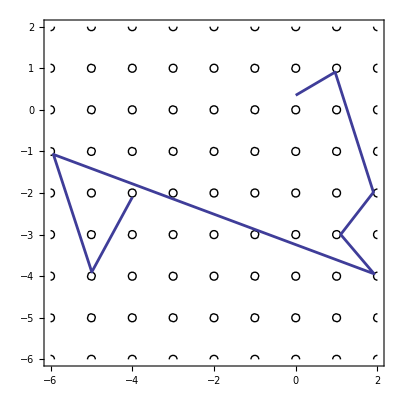

```mathematica
Show[circles,ListPlot[points,Joined->True,PlotStyle->Directive[Thickness[0.005]]]]
```

```mathematica
points:={{0,0.445},{0.94488,1.91656}}
```

```mathematica
(* Initial conditions x = (0, 0.445), v = (cos 1, sin 1), ρ = 0.1 *)
```

```mathematica
points:={{0.0,0.445},{0.94488,1.91656},{-0.971676,-0.904095},{-0.989769,-0.0994753},{-0.0924276,-4.96183},{-2.93286,-6.92589},{0.901081,-0.0146626}}
```

```mathematica
(* Classical trajectory for these initial conditions *)
```

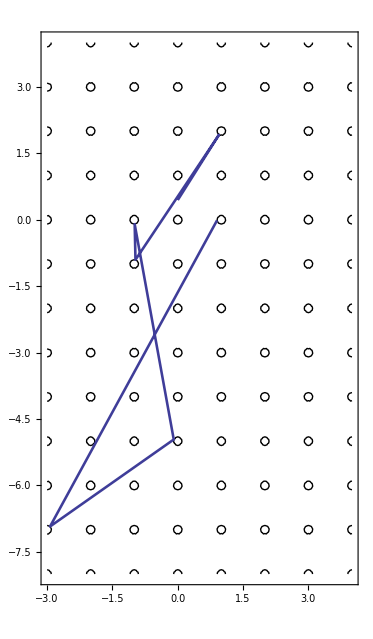

```mathematica
Show[circles,ListPlot[points,Joined->True,PlotStyle->Directive[Thickness[0.005]]]]
```

```mathematica
(* The same but with a smaller radius of obstacles ρ = 0.05 *)
```

```mathematica
points2:={{0.0,0.445},{0.971899,1.95864},{-3.99055,-4.9509},{-4.96076,-1.03099},{-4.03126,-1.03902}}
```

```mathematica
ρ:=0.05
```

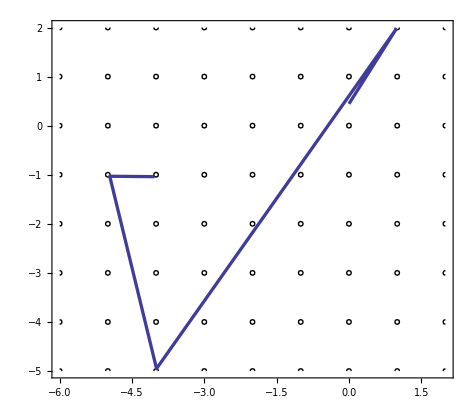

```mathematica
Show[circles,ListPlot[points2,Joined->True,PlotStyle->Directive[Thickness[0.005]]]]
```

```mathematica
(* x=0; y=0.445; vx=cos(1); vy=sin(1); r=0.1 - same classical but enlarged plot *)
```

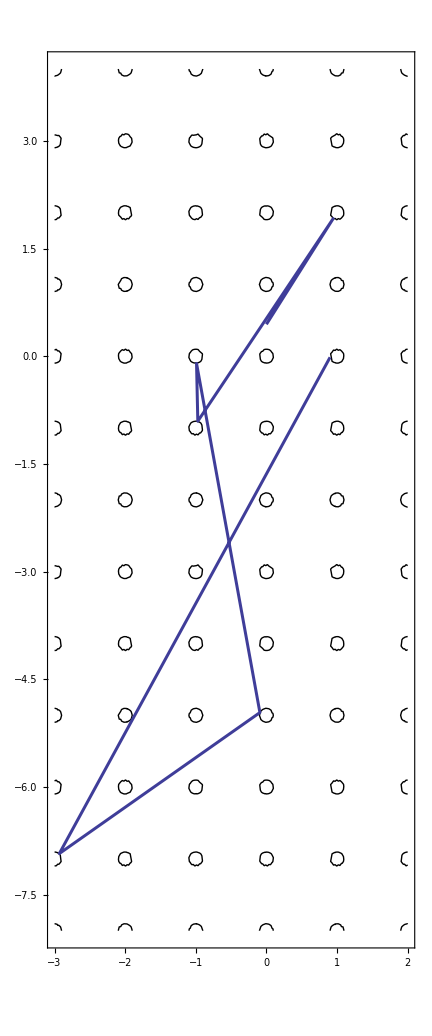

```mathematica
Show[circles,ListPlot[points,Joined->True,PlotStyle->Directive[Thickness[0.005]]]]
```

```mathematica
(*********************************************************************************)
```

```mathematica
(* Trying to find the error in first_collision() of EfficientLorentz *)
```

```mathematica
x0 := {0,0.8523674178538906}
```

```mathematica
v0 := {-0.5687431776454224,-0.8225151657457678}
```

```mathematica
k := v0[[2]]/v0[[1]]
```

```mathematica
b:=x0[[2]]-k x0[[1]]
```

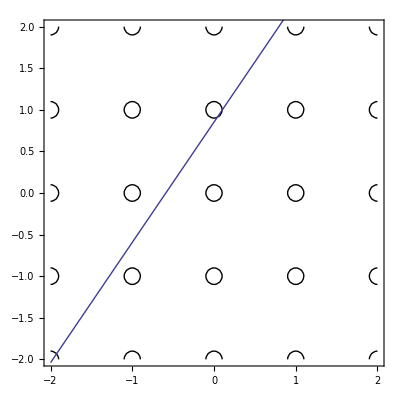

```mathematica
Show[circles,Plot[k x+b,{x,-2,2}]]
```

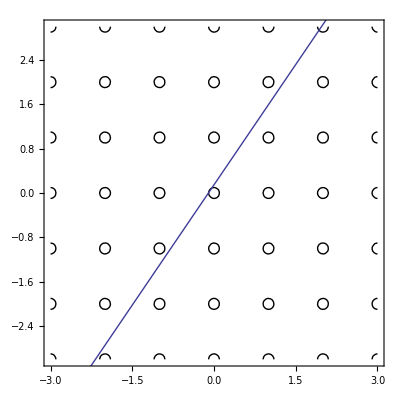

```mathematica
Show[circles,Plot[k x+1-b,{x,-3,3}]]
```

```mathematica
x0:={0,0.12}
```

```mathematica
v0={0.8,12}/Norm[{0.8,12}]
```

{0.066519,0.997785}

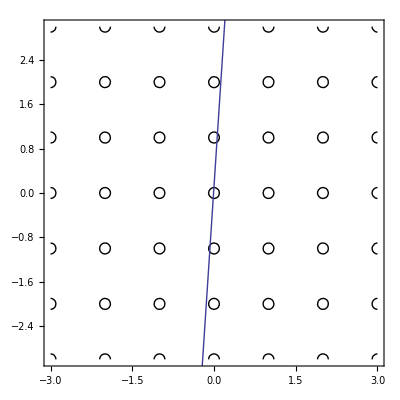

```mathematica
Show[circles,Plot[k x+b,{x,-2,2}]]
```

```mathematica
y1[x1_]:=1.2 x1+0.13
```

```mathematica
(* This formula was wrong! I found an error and fixed it. *)
```

```mathematica
dist[x_,y_,k_,b_]:=(y - k x - b)/(√(k^2+b^2))
```

```mathematica
dist[1,1,0.86,0.13]
```

0.0114973

```mathematica
dist[0,1,12,0.13]
```

0.0724957

```mathematica
dist[-1,1,-1.1,0.13]
```

-0.207646

```mathematica
dist[-1, 1, -0.9, 0.13]
```

-0.0329909

```mathematica
ϕ[b_]:=ArcTan[1-b]
```

```mathematica
l[b_]:=√(1+(1-b)^2)
```

```mathematica
dϕ[r_,b_]:=ArcSin[r/l[b]]
```

```mathematica
ψ[r_,b_]:=ArcSin[r/(1-b)]
```

```mathematica
TrigExpand[Tan[ϕ[b]-dϕ[r,b]]]
```

```mathematica
FullSimplify[-r/((1+(1-b)^2) (r/(1+(1-b)^2)-(b r)/(1+(1-b)^2)+(√(1-r^2/(1+(1-b)^2)))/(√(1+(1-b)^2))))+(√(1-r^2/(1+(1-b)^2)))/(√(1+(1-b)^2) (r/(1+(1-b)^2)-(b r)/(1+(1-b)^2)+(√(1-r^2/(1+(1-b)^2)))/(√(1+(1-b)^2))))-(b √(1-r^2/(1+(1-b)^2)))/(√(1+(1-b)^2) (r/(1+(1-b)^2)-(b r)/(1+(1-b)^2)+(√(1-r^2/(1+(1-b)^2)))/(√(1+(1-b)^2))))]
```

```mathematica
FullSimplify[(-1+b+√(2+(-2+b) b) r √(1-r^2/(2+(-2+b) b)))/(-1+r^2),b>0&&b<1&&r>0]
```

(-1+b+r √(2+(-2+b) b-r^2))/(-1+r^2)

```mathematica
TrigExpand[Tan[ϕ[b]+dϕ[r,b]]]
```

```mathematica
FullSimplify[r/((1+(1-b)^2) (-r/(1+(1-b)^2)+(b r)/(1+(1-b)^2)+(√(1-r^2/(1+(1-b)^2)))/(√(1+(1-b)^2))))+(√(1-r^2/(1+(1-b)^2)))/(√(1+(1-b)^2) (-r/(1+(1-b)^2)+(b r)/(1+(1-b)^2)+(√(1-r^2/(1+(1-b)^2)))/(√(1+(1-b)^2))))-(b √(1-r^2/(1+(1-b)^2)))/(√(1+(1-b)^2) (-r/(1+(1-b)^2)+(b r)/(1+(1-b)^2)+(√(1-r^2/(1+(1-b)^2)))/(√(1+(1-b)^2)))),b>0&&b<1&&r>0]
```

(r-(-1+b) √(2+(-2+b) b-r^2))/((-1+b) r+√(2+(-2+b) b-r^2))

```mathematica
TrigExpand[Tan[π/2-ψ[r,b]]]
```

```mathematica
FullSimplify[(√(1-r^2/(1-b)^2))/r-(b √(1-r^2/(1-b)^2))/r,b>0&&b<1&&r>0]
```

(√((-1+b)^2-r^2))/r

```mathematica
(******************************)
```

```mathematica
(* Another test: classical: collisions([0, 0.3], [cos(1.2), sin(1.2)], 0.1, 40) *)
```

```mathematica
circles:=ContourPlot[Evaluate[Flatten[Table[(x-n)^2+(y-m)^2==ρ^2,{n,-3,25},{m,0,3}]]],{x,-3,25},{y,0,3},Axes->True,AspectRatio->Automatic,ContourStyle->Black]
```

```mathematica
points:={{0.0,0.3},{1.0110656406928884,2.900614127784398},{2.9219146792616817,0.062471454962998996},{-1.9157883662346256,1.946070409434463},{-1.0335723144172106,1.094196070537321},{-0.9350814498167989,1.923936987687108},{19.969454049802543,1.0952205068592602},{21.005610680123482,1.9001575227242835},{23.964414084951475,0.093453960056057}}
```

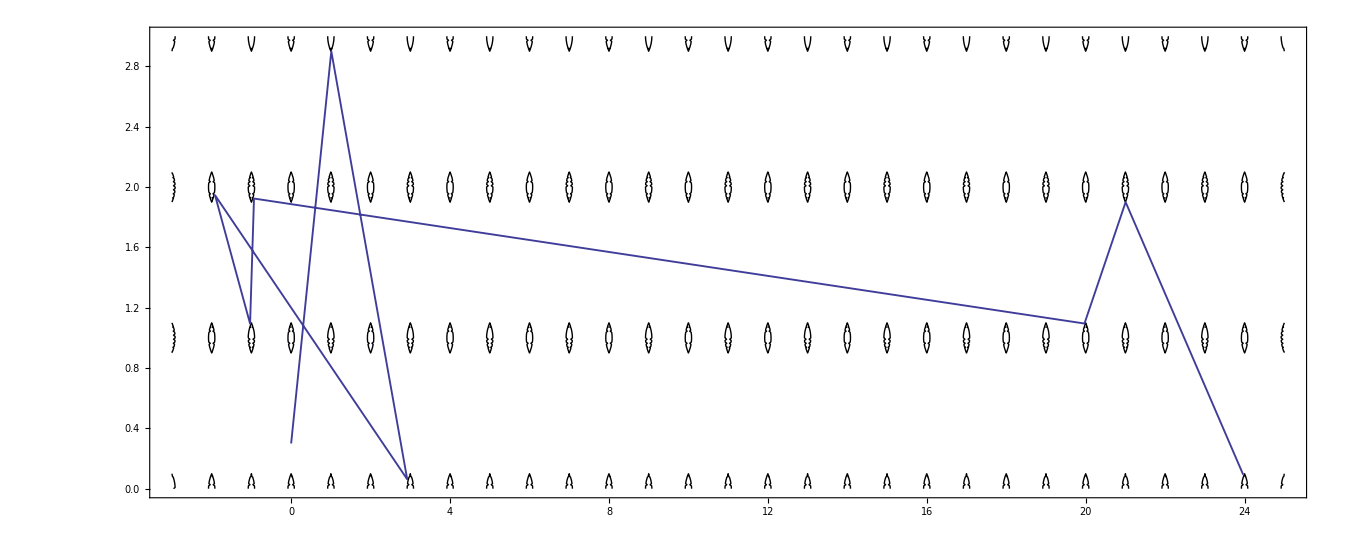

```mathematica
Show[circles,ListPlot[points,Joined->True,PlotStyle->Directive[Thickness[0.001]]]]
```

```mathematica
(* Finding out why and how the algorithm diverges *)
```

```mathematica
x0:={-25.9220385027411,24.062625912729082}
```

```mathematica
v0:={0.967026401228994,-0.2546761459699459}
```

```mathematica
k:=v0⟦2⟧/v0⟦1⟧
```

```mathematica
b:=x0⟦2⟧-k x0⟦1⟧
```

```mathematica
(* Stuff happens in the (-26, 25) neighborhood *)
```

```mathematica
circles:=ContourPlot[Evaluate[Flatten[Table[(x-n)^2+(y-m)^2==ρ^2,{n,-27,-23},{m,23,26}]]],{x,-27,-23},{y,23,26},Axes->True,AspectRatio->Automatic,ContourStyle->Black]
```

```mathematica
points:={{-23.91094892340575,24.045496216957076},{-24.035703610028186,24.906590941387062},{-24.999698062403922,24.099999544167403},{-25.956133158899803,24.91013510000067},{-25.9220385027411,24.062625912729082}}
```

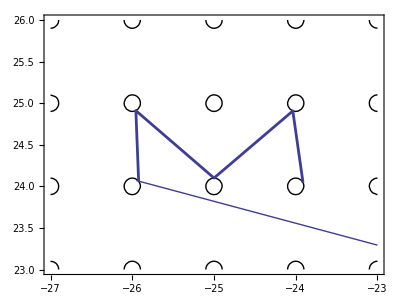

```mathematica
Show[circles,ListPlot[points,Joined->True,PlotStyle->Directive[Thickness[0.005]]],Plot[k x+b,{x,-25.95,-23}]]
```

```mathematica
dist[-26,24,k,b]
```

-0.00482416

```mathematica
dist[-25,24,k,b]
```

0.0104539

```mathematica
(* How is this possible?! The distance is clearly greater than 0.1! *)
```

```mathematica
line[x_]:=k x+b
```

```mathematica
line[-25]
```

23.8198

```mathematica
24-k*(-25)-b
```

0.180202

```mathematica
√(k^2+b^2)
```

17.2378

```mathematica
line[-25]-24
```

-0.180202

```mathematica
(* Error found in formula p. 69 UNAM notebook 1 *)
```

```mathematica
ρ:=0.1
```

```mathematica
circles:=ContourPlot[Evaluate[Flatten[Table[(x-n)^2+(y-m)^2==ρ^2,{n,-27,2},{m,-8,27}]]],{x,-27,2},{y,-8,27},Axes->True,AspectRatio->Automatic,ContourStyle->Black,PlotRange->{{-27,2},{-8,27}}]
```

```mathematica
points:={{0.0,0.445},{0.9448796725624946,1.9165629009182235},{-0.9716764156856601,-0.9040949710829063},{-0.9897690501214653,-0.0994752615708192},{-0.09242759468202599,-4.9618275001958825},{-2.9328562249389405,-6.925893903958246},{0.9010807499311531,-0.014662263325179836},{-23.91094892340575,24.045496216957076},{-24.035703610028186,24.906590941387062},{-24.999698062403922,24.099999544167403},{-25.956133158899803,24.91013510000067},{-25.9220385027411,24.062625912729082},{-22.085304699895232,23.05218340900884},{-22.90529612309773,23.967888075428597},{-17.071782715191617,25.069622135845716},{-16.937658041096565,25.921811252983037},{-4.091286280011369,25.04082664671126},{-4.975737295694259,25.90298803589365},{-5.900026892297164,22.99768100533914},{-5.099634509442279,20.008541927662797},{-5.981885711413208,18.09834567885268}}
```

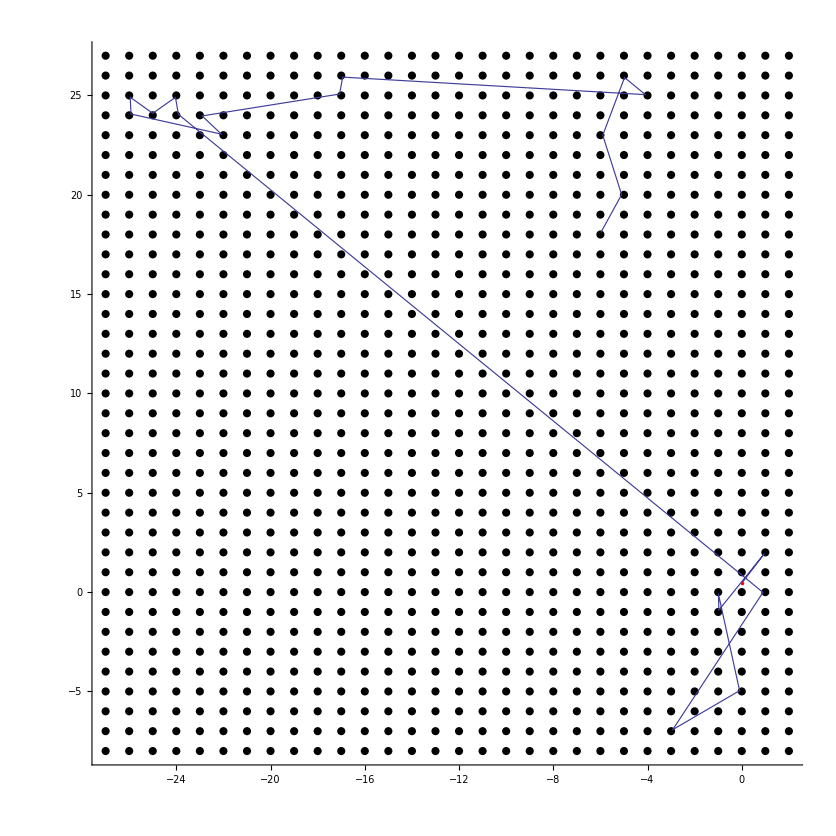

```mathematica
Show[ListPlot[Table[{n,m},{n,-27,2},{m,-8,27}],PlotStyle->Directive[PointSize->0.007,Black],AspectRatio->1],ListPlot[points,Joined->True,PlotStyle->Directive[Thickness[0.001]]],ListPlot[{{0,0.445}},PlotStyle->Directive[PointSize->0.003,Red]]]
```

```mathematica
circles:=ContourPlot[Evaluate[Flatten[Table[(x-n)^2+(y-m)^2==ρ^2,{n,-2,2},{m,-2,2}]]],{x,-2,2},{y,-2,2},Axes->True,AspectRatio->Automatic,ContourStyle->Black,PlotRange->{{-2,2},{-2,2}}]
```

```mathematica
x0:={0, 0.445}
```

```mathematica
v0:={0.215, 0.336}
```

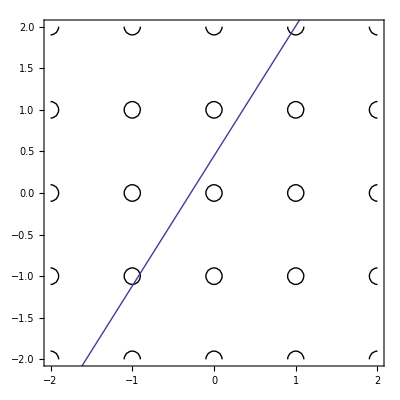

```mathematica
Show[circles,Plot[v0[[2]]/v0[[1]] x+x0[[2]],{x,-2,2}]]
```

```mathematica
(* Error when the initial position has an integer coordinate (in a particular case) *)
```

```mathematica
x0:={-2.12565,-3}
```

```mathematica
v0:={-0.536682,-0.843784}
```

```mathematica
ρ:=0.1
```

```mathematica
circles:=ContourPlot[Evaluate[Flatten[Table[(x-n)^2+(y-m)^2==ρ^2,{n,-6,-1},{m,-6,-1}]]],{x,-6,-1},{y,-6,-1},Axes->True,AspectRatio->Automatic,ContourStyle->Black,PlotRange->{{-6,-1},{-6,-1}}]
```

```mathematica
line[x]
```

0.341997+1.57222 x

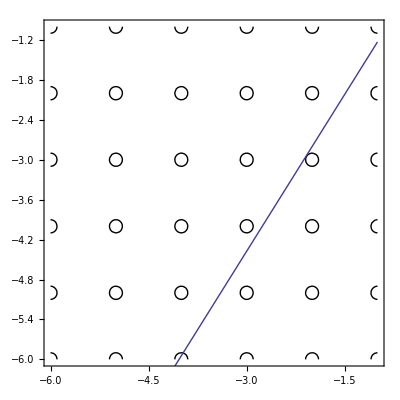

```mathematica
Show[circles,Plot[line[x],{x,-6,-1}]]
```

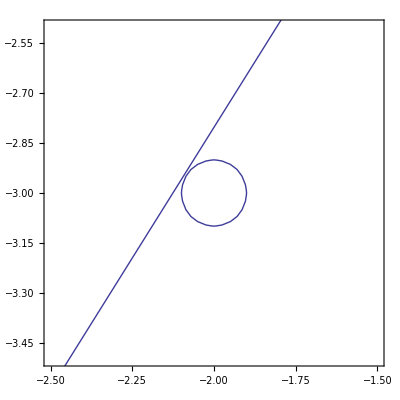

```mathematica
Show[ContourPlot[(x+2)^2+(y+3)^2==ρ^2,{x,-2.5,-1.5},{y,-3.5,-2.5}],Plot[line[x],{x,-2.5,-1.5}]]
```

```mathematica
(*********************************************************)
```

```mathematica
(* 3D version *)
```

```mathematica
x0 := {0.5,0.5,0.5}
```

```mathematica
v0:={0.1112,0.19779,0.0669}
```

```mathematica
Show[spheres[0.1,0,5,0,5,0,5],line[x0,v0,20]]
```

-Graphics3D-

```mathematica
x0:={0,0.445,0.342}
```

```mathematica
v0:={0.451207,0.541449,0.709398}
```

```mathematica
Show[spheres[0.1,2,4,3,5,4,6],line[x0,v0,4,7]]
```

-Graphics3D-

```mathematica
(* This line intersects the ball (3,4,5), but not through the center *)
```

```mathematica
v1:={-0.4512069325775071,-0.5414489190929208,-0.7093978939968069}
```

```mathematica
x1:={2.92769084745365,3.9582329100898943,4.944982736974214}
```

```mathematica
Show[spheres[0.1,-6,-1,-6,-1,-6,-1],line[x1,v1,8,16]]
```

-Graphics3D-

```mathematica
Show[spheres[0.1,-38,-36,-45,-43,-59,-57],line[x1,v1,87,90]]
```

-Graphics3D-

```mathematica
(* Distance between 3D line x⃗ = (x⃗)_0 + (v⃗)_0 t and a point p⃗ *)
```

```mathematica
distance[x0_,v0_,p_]:=Norm[x0-p-((x0-p).v0)v0]
```

```mathematica
p:={-37,-44,-58}
```

```mathematica
distance[x1,v1,p]
```

0.0994014

```mathematica
(* Less than 0.1, so this ball gets hit *)
```

```mathematica
x2:={-37.06038678750248,-44.027513426667056,-57.92519059385232}
```

```mathematica
v2:={0.4512069325775123,0.5414489190929171,0.7093978939968061}
```

```mathematica
(****)
```

```mathematica
Show[spheres[0.2,0,4,0,4,0,4],line[x0,v0,0,5]]
```

-Graphics3D-

```mathematica
x0 :={0.445,0.342}
```

```mathematica
v0:={0.60672,0.794915}
```

```mathematica
ρ:=0.2
```

```mathematica
circles:=ContourPlot[Evaluate[Flatten[Table[(x-n)^2+(y-m)^2==ρ^2,{n,-1,3},{m,-1,3}]]],{x,-1,3},{y,-1,3},Axes->True,AspectRatio->Automatic,ContourStyle->Black,PlotRange->{{-1,3},{-1,3}}]
```

```mathematica
line2d[x_,x0_,v0_]:=v0[[2]]/v0[[1]] x+x0[[2]]-v0[[2]]/v0[[1]] x0[[1]]
```

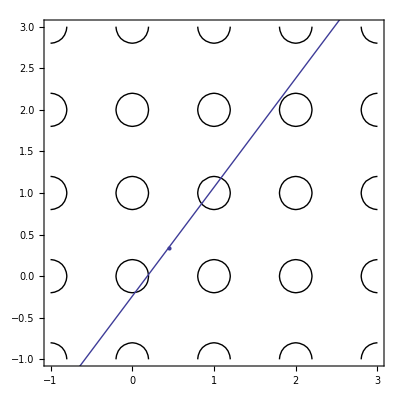

```mathematica
Show[circles,Plot[line[x,x0,v0],{x,-1,3}],ListPlot[{x0}]]
```

```mathematica
x0:={0.0,0.445};v0:={0.640184,0.768222}
```

```mathematica
v0
```

{0.640184,0.768222}

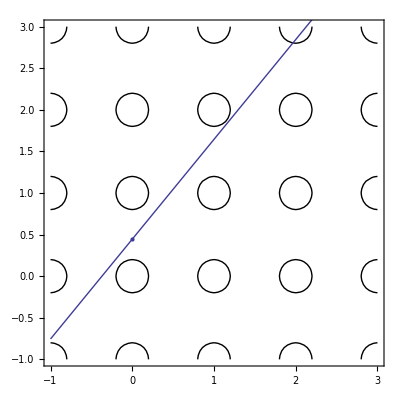

```mathematica
Show[circles,Plot[line[x,x0,v0],{x,-1,3}],ListPlot[{x0}]]
```

```mathematica
x0:={0.445,0.342};v0:={0.60672,0.794915};ρ:=0.1
```

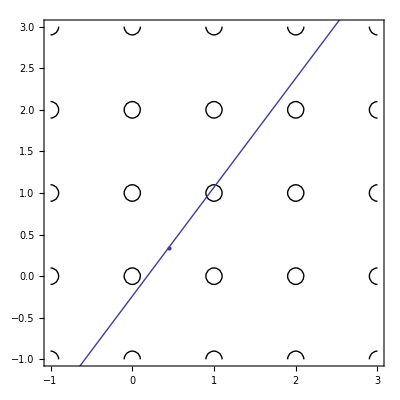

```mathematica
Show[circles,Plot[line[x,x0,v0],{x,-1,3}],ListPlot[{x0}]]
```

```mathematica
x0:={-3.96176770832104644011,9.00000000007393451476,-17.2248540924254255422}
```

```mathematica
v0:={0.492197878294012166407,0.739345146123457909362,-0.459467086423560331943}
```

```mathematica
ρ:=0.2
```

```mathematica
Show[spheres[0.2,-3,1,11,16,-21,-18],line[x0,v0,0,5]]
```

-Graphics3D-

```mathematica
p:={-2,12,-19}
```

```mathematica
distance[x0,v0,p]
```

0.0761529158922801

```mathematica
x0:={-1.81694,12.2218,-19.227}
```

```mathematica
v0:={0.492197878294012166407,0.739345146123457909362,-0.459467086423560331943}
```

```mathematica
Show[spheres[0.2,-2,0,12,15,-21,-19],line[x0,v0,0,5],ListPointPlot3D[{{-1.81694,12.2218,-19.227}}]]
```

-Graphics3D-

```mathematica
Norm[x0-{-2,12,-19}]
```

0.366381

```mathematica
x0:={-31.5646794874135777267,10.0000000000071421636,-8.86136400925839916656}
```

```mathematica
v0:={-0.995170604930726595226,0.0714216332842911117977,0.0673380826933461717346}
```

```mathematica
Show[spheres[0.2,-32,-30,10,11,-9,-8],line[x0,v0,0,1],ListPointPlot3D[{x0}]]
```

-Graphics3D-

```mathematica
distance[x0,v0,{-32,10,-9}]
```

0.1704328213849556

```mathematica
x0:={-31.5647,10.0}
```

```mathematica
v0:={-0.997435,0.0715841}
```

```mathematica
ρ:=0.2
```

```mathematica
circles:=ContourPlot[Evaluate[Flatten[Table[(x-n)^2+(y-m)^2==ρ^2,{n,-33,-30},{m,9,11}]]],{x,-33,-30},{y,9,11},Axes->True,AspectRatio->Automatic,ContourStyle->Black,PlotRange->{{-33,-30},{9,11}}]
```

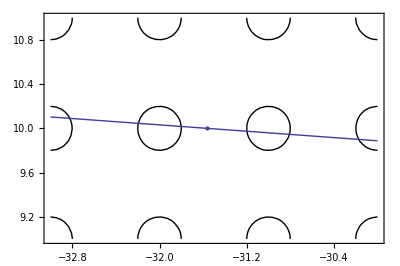

```mathematica
Show[circles,Plot[line2d[x,x0,v0],{x,-33,-30}],ListPlot[{x0}]]
```

```mathematica
(******************************************************************************)
```

```mathematica
(* Resolving the problem: C and E agree on the first collision and the immediate-afterward coord and speed, but the E misses obstacles which C finds. Need to see simulation *)
```

```mathematica
x0:={2.88124933590079817603,3.90250303447010145775,4.87196632673995360611}
```

```mathematica
v0:={-0.719660173353565737683,-0.419859303753652908205,-0.552998553289439927704}
```

```mathematica
lorentz3d[0.2,-2,3,0,4,0,5,0,8]
```

-Graphics3D-

```mathematica
lorentz3dnostart[0.2,-2,1,0,2,0,2,5,8]
```

-Graphics3D-

```mathematica
(* David Sanders' idea: take x={0,0,0} and v = {2/3, 2/3, 1/3}. It hits (2,2,1). In xy-plane, it "hits" both (1,1) and (2,2), and in yz- and xz-planes it "hits" (2,1). The initial values are too "exact", so the E algorithm may stall. We "smudge" the values a bit. *)
```

```mathematica
v0:={2/3, 2/3, 1/3}
```

```mathematica
x0:=v0*0.8
```

```mathematica
lorentz3d[x0,v0,0.2,0,2,0,2,0,2,0,3]
```

-Graphics3D-

```mathematica
x0:={10.0764053422964544949,26.029067229247587742,6.81746967415678619328}
```

```mathematica
v0:={0.837062156955717057171,-0.493583634870910865824,-0.236013009769084225237}
```

```mathematica
lorentz3d[x0,v0,0.2,8,10,25,28,4,7,0,5]
```

-Graphics3D-

```mathematica
dist3d[x_,v_,point_]:=Norm[Cross[point-x,v]]/Norm[v]
```

```mathematica
dist3d[x0,v0,{10,26,7}]
```

0.17719445859133287

```mathematica
x0:={16.8289990492993435135,22.0452392128352392103,4.90666143090062079925}
```

```mathematica
v0:={-0.388641823164963131992,-0.169475879050012219677,-0.905668515356054074767}
```

```mathematica
(* Zoom in at the arguable place *)
```

```mathematica
lorentz3dnostart[x0,v0,0.2,12,14,20,22,-6,-2,7,12]
```

-Graphics3D-